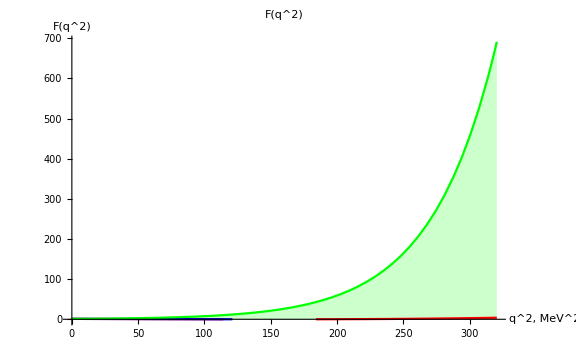

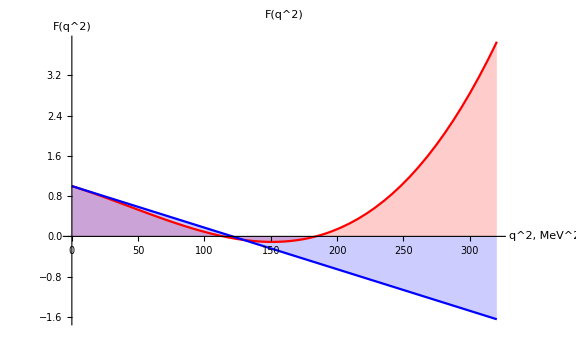

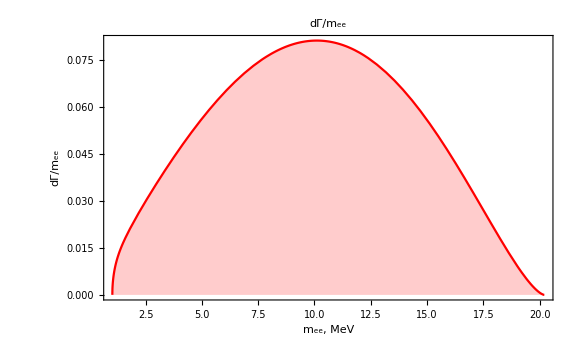

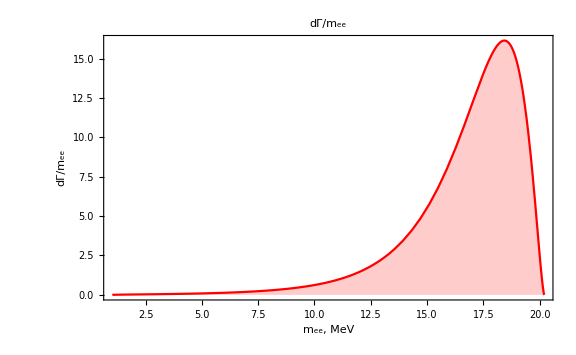

```mathematica
qmax=17.9;
lambda1=20.0;
f1=-3.323; f2=-5.759; f3=17.95; 
FF1[q2_]:=1+f1*(q2/lambda1^2)+f2*(q2/lambda1^2)^2+f3*(q2/lambda1^2)^3;
g1=-3.305; 
FF2[q2_]:=1+g1*(q2/lambda1^2);
lambda2=7.0;
FF3[q2_]:=Exp[q2/lambda2^2];
Plot[{FF1[q2],FF2[q2],FF3[q2]},                  {q2,0,qmax^2},
PlotLabel->"F(q^2)",
FrameLabel->{"q^2","F(q^2)"},
Filling->Axis,
PlotRange->{{0,qmax^2},{0,All}},
Axes->True,AxesLabel->{"q^2, MeV^2","F(q^2)"},
PlotStyle->{Red,Blue,Green},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
Plot[{FF1[q2],FF2[q2]},                  {q2,0,qmax^2},
PlotLabel->"F(q^2)",
FrameLabel->{"q^2","F(q^2)"},
Filling->Axis,
PlotRange->{{0,qmax^2},{-2,All}},
Axes->True,AxesLabel->{"q^2, MeV^2","F(q^2)"},
PlotStyle->{Red,Blue,Green},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
qmax2=20.21;
Plot[dgdq[q],                     {q,qmin,qmax2},
PlotLabel->"dΓ/m_ee",
PlotRange->{{qmin,qmax2},{0,All}},
Frame ->True, FrameLabel->{"m_ee, MeV","dΓ/m_ee"},
Filling->Axis,
PlotStyle->{Blue,Red},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
Plot[dgdq[q]FF3[q^2],                     {q,qmin,qmax2},
PlotLabel->"dΓ/m_ee",
PlotRange->{{qmin,qmax2},{0,All}},
Frame ->True, FrameLabel->{"m_ee, MeV","dΓ/m_ee"},
Filling->Axis,
PlotStyle->{Blue,Red},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
```